# 奇异值分解

```mathematica
A={{1,0,0,0},{0,0,0,4},{0,3,0,0},{0,0,0,0},{2,0,0,0}};
{U,Σ,V}=SingularValueDecomposition[A];
A.Transpose@A//MatrixForm
Transpose@A.A//MatrixForm
U//MatrixForm
Σ//MatrixForm
V//MatrixForm
```

(1 | 0 | 0 | 0 | 2
0 | 16 | 0 | 0 | 0
0 | 0 | 9 | 0 | 0
0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 4)

(5 | 0 | 0 | 0
0 | 9 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 16)

(0 | 0 | -1/(√5) | -2/(√5) | 0
-1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1
0 | 0 | -2/(√5) | 1/(√5) | 0)

(4 | 0 | 0 | 0
0 | 3 | 0 | 0
0 | 0 | √5 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0)

```mathematica
U.Σ.Transpose@V//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 4
0 | 3 | 0 | 0
0 | 0 | 0 | 0
2 | 0 | 0 | 0)

# 紧奇异值分解

```mathematica
A={{1,0,0,0},{0,0,0,4},{0,3,0,0},{0,0,0,0},{2,0,0,0}};
r=MatrixRank[A];
{U,Σ,V}=SingularValueDecomposition[A,UpTo[r]];
A.Transpose@A//MatrixForm
Transpose@A.A//MatrixForm
U//MatrixForm
Σ//MatrixForm
V//MatrixForm
```

(1 | 0 | 0 | 0 | 2
0 | 16 | 0 | 0 | 0
0 | 0 | 9 | 0 | 0
0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 4)

(5 | 0 | 0 | 0
0 | 9 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 16)

(0 | 0 | -1/(√5)
-1 | 0 | 0
0 | 1 | 0
0 | 0 | 0
0 | 0 | -2/(√5))

(4 | 0 | 0
0 | 3 | 0
0 | 0 | √5)

(0 | 0 | -1
0 | 1 | 0
0 | 0 | 0
-1 | 0 | 0)

```mathematica
U.Σ.Transpose@V//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 4
0 | 3 | 0 | 0
0 | 0 | 0 | 0
2 | 0 | 0 | 0)

# 截断奇异值分解

```mathematica
A={{1,0,0,0},{0,0,0,4},{0,3,0,0},{0,0,0,0},{2,0,0,0}};
k=2;
{U,Σ,V}=SingularValueDecomposition[A,UpTo[k]];
A.Transpose@A//MatrixForm
Transpose@A.A//MatrixForm
U//MatrixForm
Σ//MatrixForm
V//MatrixForm
```

(1 | 0 | 0 | 0 | 2
0 | 16 | 0 | 0 | 0
0 | 0 | 9 | 0 | 0
0 | 0 | 0 | 0 | 0
2 | 0 | 0 | 0 | 4)

(5 | 0 | 0 | 0
0 | 9 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 16)

(0 | 0
-1 | 0
0 | 1
0 | 0
0 | 0)

(4 | 0
0 | 3)

(0 | 0
0 | 1
0 | 0
-1 | 0)

```mathematica
U.Σ.Transpose@V//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 4
0 | 3 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

# 潜在语义分析

```mathematica
X={{0,0,1,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,1},{0,1,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,0,1},{1,0,0,0,0,1,0,0,0},{1,1,1,1,1,1,1,1,1},{1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1},{0,0,0,0,0,2,0,0,1},{1,0,1,0,0,0,0,1,0},{0,0,0,1,1,0,0,0,0}};
k=3;
{U,Σ,V}=SingularValueDecomposition[X,UpTo[k]];
X.Transpose@X//MatrixForm
Transpose@X.X//MatrixForm
U//MatrixForm//N
Σ//MatrixForm//N;
V//MatrixForm//N;
Σ.Transpose@V//MatrixForm//N
```

(2 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 1
0 | 2 | 0 | 1 | 1 | 2 | 0 | 1 | 3 | 0 | 0
0 | 0 | 2 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 2 | 0 | 2 | 0 | 2 | 1 | 0 | 0
0 | 1 | 0 | 0 | 2 | 2 | 1 | 0 | 2 | 1 | 0
2 | 2 | 2 | 2 | 2 | 9 | 2 | 2 | 3 | 3 | 2
1 | 0 | 0 | 0 | 1 | 2 | 2 | 0 | 0 | 2 | 0
0 | 1 | 0 | 2 | 0 | 2 | 0 | 2 | 1 | 0 | 0
0 | 3 | 0 | 1 | 2 | 3 | 0 | 1 | 5 | 0 | 0
1 | 0 | 1 | 0 | 1 | 3 | 2 | 0 | 0 | 3 | 0
1 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2)

(4 | 1 | 3 | 1 | 1 | 2 | 1 | 2 | 1
1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 1
3 | 1 | 4 | 2 | 1 | 1 | 1 | 2 | 1
1 | 1 | 2 | 3 | 2 | 1 | 1 | 1 | 1
1 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1
2 | 1 | 1 | 1 | 1 | 7 | 1 | 1 | 4
1 | 1 | 1 | 1 | 1 | 1 | 3 | 1 | 3
2 | 2 | 2 | 1 | 1 | 1 | 1 | 3 | 1
1 | 1 | 1 | 1 | 1 | 4 | 3 | 1 | 5)

(0.152836 | -0.266034 | 0.0445032
0.237464 | 0.378263 | -0.0859589
0.130265 | -0.174284 | 0.0690143
0.184404 | 0.193948 | 0.44569
0.216123 | 0.0872725 | -0.460119
0.740097 | -0.211147 | 0.210753
0.176876 | -0.297912 | -0.283203
0.184404 | 0.193948 | 0.44569
0.363078 | 0.588541 | -0.341198
0.250194 | -0.415577 | -0.284353
0.122936 | -0.143178 | 0.234491)

(1.38329 | 0.870362 | 1.32 | 1.01587 | 0.863033 | 1.91984 | 1.10891 | 1.12056 | 1.70945
-0.837363 | -0.385431 | -1.19067 | -0.62036 | -0.354325 | 1.43147 | 0.17675 | -0.801008 | 1.14355
-0.816921 | 0.279767 | -0.312299 | 0.489748 | 0.445244 | -1.01772 | 1.10213 | -0.00458523 | 0.674975)

# 主成分分析

```mathematica
X={{1,2,4,5,7,8},{2,3,5,6,8,7}};
Covariance[X//Transpose]//MatrixForm
X=Table[Table[X[[i,j]]-Mean[X[[i]]],{j,Length[X[[1]]]}],{i,Length[X]}]
1/(Length[X[[1]]]-1)X.Transpose@X//MatrixForm
X=Table[X[[i]]/StandardDeviation[X[[i]]],{i,Length[X]}]
Rx=Covariance[X//Transpose]//MatrixForm
```

(15/2 | 61/10
61/10 | 161/30)

{{-7/2,-5/2,-1/2,1/2,5/2,7/2},{-19/6,-13/6,-1/6,5/6,17/6,11/6}}

(15/2 | 61/10
61/10 | 161/30)

{{-7/(√30),-√(5/6),-1/(√30),1/(√30),√(5/6),7/(√30)},{-19 √(5/966),-13 √(5/966),-√(5/966),5 √(5/966),17 √(5/966),11 √(5/966)}}

(1 | 1/5 (5 √(7/23)+26/(√161))
1/5 (5 √(7/23)+26/(√161)) | 1)

```mathematica
R={{1.,0.44,0.29,0.33},{0.44,1.,0.35,0.32},{0.29,0.35,1.,0.60},{0.33,0.32,0.60,1.}};
R//MatrixForm
{λ,α}=Eigensystem[R];
λ//MatrixForm
α//MatrixForm
set=0.7;
For[t=0;tmp={},t<Length[λ],t++,If[Total[Table[λ[[i]],{i,t}]]/(λ//Total)>set,AppendTo[tmp,t]]];
k=tmp[[1]]
ralpha=Table[α[[i]],{i,k}];
ralpha//MatrixForm
contributetoall=Table[λ[[i]]/Total[λ],{i,k}]
load=Table[Table[Sqrt[λ[[i]]/R[[i,i]]]*ralpha[[i,j]],{j,Length[R[[1]]]}],{i,k}]
contributetosiglex=Table[Table[load[[i,j]]^2,{i,k}]//Total,{j,Length[R[[1]]]}]
```

(1. | 0.44 | 0.29 | 0.33
0.44 | 1. | 0.35 | 0.32
0.29 | 0.35 | 1. | 0.6
0.33 | 0.32 | 0.6 | 1.)

(2.17017
0.871005
0.566179
0.39265)

(-0.459908 | -0.476312 | -0.52875 | -0.53107
-0.567909 | -0.490907 | 0.475571 | 0.458609
0.666559 | -0.715354 | -0.112862 | 0.176723
-0.147185 | 0.142849 | -0.693915 | 0.690226)

2

(-0.459908 | -0.476312 | -0.52875 | -0.53107
-0.567909 | -0.490907 | 0.475571 | 0.458609)

{0.542541,0.217751}

{{-0.677512,-0.701679,-0.778927,-0.782344},{-0.530017,-0.458152,0.443839,0.428009}}

{0.73994,0.702256,0.80372,0.795254}

# 聚类分析

```mathematica
data={{3,1},{3,2},{4,1},{4,2},{1,3},{1,4},{2,3},{2,4}};
```

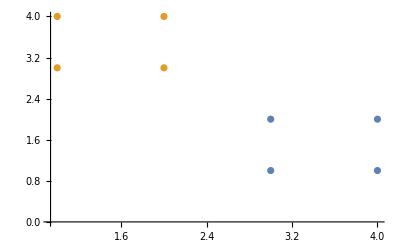

```mathematica
ListPlot[FindClusters[data, 2, Method->"KMeans"]]
```